# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Constants

```mathematica
ℏ=1;
m=1;
ω=1;
L=2;
```

```mathematica
tollerance=10^-6;
```

```mathematica
sel[k_]:={#⟦1⟧,#⟦2,k⟧}&
```

#### Reduce pure functions

```mathematica
mergeF[expr_]:=Function@@(Hold[expr]/.Function[body_]:>body)
```

#### Root finding function

```mathematica
findRoot:=Function[{f,min,max,d},
Block[{sgb,sgt,sgc,c,mn,mx},
sgb=Sign[f[min]];
sgt=Sign[f[max]];
mn=min;
mx=max;
c=mn;
While[mx-mn>d,
c=0.5(mn+mx);
sgc=Sign[f[c]];
If[sgc==sgb,mn=c,mx=c];
];
c
]
];
```

#### Method of shooting

```mathematica
findEigenvalues:=Function[{V,dE,emax,tollerance,L},
Block[{i,ψ,Ψ,sol,en,f,sgb,sgt,eb=0,et=dE,root,ev},
f:=Function[{e},
NDSolve[{-ℏ^2/(2m)ψ''[x]==(e-V[x])ψ[x],ψ[-L/2]==0,ψ'[-L/2]==1},ψ,{x,-L/2,L/2}]⟦1,1,2⟧[L/2]
];
ev=Reap[
sgb=Sign[f[eb]];
For[i=0,et≤emax,++i,
sgt=Sign[f[et]];
If[sgb≠sgt,
root=findRoot[f,eb,et,tollerance];
Sow[root];
];
eb=et;
et+=dE;
sgb=sgt;
]
]⟦2⟧;
If[Length[ev]>0,ev⟦1⟧,{}]
]
]
```

```mathematica
findEigenvaluesInf:=Function[{V,dE,emin,emax,tollerance,L,even},
Block[{i,ψ,Ψ,sol,en,f,sgb,sgt,eb=emin,et=dE,root,ev},
If[even,
f:=Function[{e}, NDSolve[{-ℏ^2/(2m)ψ''[x]==(e-V[x])ψ[x],ψ[0]==0,ψ'[0]==1},ψ,{x,-L-1,L+1}]⟦1,1,2⟧[L]
],
f:=Function[{e}, NDSolve[{-ℏ^2/(2m)ψ''[x]==(e-V[x])ψ[x],ψ[0]==1,ψ'[0]==0},ψ,{x,-L-1,L+1}]⟦1,1,2⟧[L]
]
];
ev=Reap[
sgb=Sign[f[eb]];
For[i=0,et≤emax,++i,
sgt=Sign[f[et]];
If[sgb≠sgt,
root=findRoot[f,eb,et,tollerance];
Sow[root];
];
eb=et;
et+=dE;
sgb=sgt;
]
]⟦2⟧;
If[Length[ev]>0,ev⟦1⟧,{}]
]
]
```

```mathematica
findAllEigenvaluesInf:=Function[{v,step,emin,emax,tollerance,l},
Block[{eigenvaluesEven,eigenvaluesOdd,eig},
eigenvaluesEven=findEigenvaluesInf[v,step,emin,emax,tollerance,l,True];
eigenvaluesOdd=findEigenvaluesInf[v,step,emin,emax,tollerance,l,False];
Union[eigenvaluesEven,eigenvaluesOdd]
]
]
```

#### Get the eigenfunction

```mathematica
findFunction:=Function[{e,V,L},
Block[{ψ,f,g,norm},
NDSolve[{-ℏ^2/(2m)ψ''[x]==(e-V[x])ψ[x],ψ[-L/2]==0,ψ'[-L/2]==1},ψ,{x,-L/2,L/2}]⟦1,1,2⟧]
]
```

```mathematica
findFunctionInf:=Function[{e,V,L,even},
Block[{ψ,f,g,norm},
If[even,NDSolve[{-ℏ^2/(2m)ψ''[x]==(e-V[x])ψ[x],ψ[0]==0,ψ'[0]==1},ψ,{x,-L-1,L+1}]⟦1,1,2⟧,NDSolve[{-ℏ^2/(2m)ψ''[x]==(e-V[x])ψ[x],ψ[0]==1,ψ'[0]==0},ψ,{x,-L-1,L+1}]⟦1,1,2⟧]
]
]
```

#### Make transition matrix from the energy levels and temperature

```mathematica
MakeTransitionMatrix:=Function[{energies,β},
Block[{l,T},
l=Length[energies]-1;
T=Table[
Switch[j-k,
1,0.5Exp[-β(energies⟦j⟧-energies⟦k⟧)],
0,0.5(1.0-Exp[-β(energies⟦j+1⟧-energies⟦k⟧)]),
-1,0.5,
_,0.
]
,{k,1,l},{j,1,l}];
T⟦1,1⟧=1-T⟦1,2⟧;
T⟦l,l⟧=0.5;
T
]
]
```

```mathematica
MakeTransitionMatrix:=Function[{eigenvalues,β},
Block[{n=Length[eigenvalues]},
Table[Switch[i,
(* Bottom case *)
1,Switch[j,
1,1-0.5 Exp[-β(eigenvalues⟦i+1⟧-eigenvalues⟦i⟧)],
2,0.5 Exp[-β(eigenvalues⟦i+1⟧-eigenvalues⟦i⟧)],
_,0
],
(* Top case *)
n,Switch[j,
n,1/2,
n-1,1/2,
_,0
],
(* Generic case *)
_,Switch[j-i,
-1,0.5,
0,0.5(1- Exp[-β(eigenvalues⟦i+1⟧-eigenvalues⟦i⟧)]),
1,0.5 Exp[-β(eigenvalues⟦i+1⟧-eigenvalues⟦i⟧)],
_,0
]],
{i,1,n},{j,1,n}]//N
]
]
```

#### Eigenfunctions for the harmonic oscillator - k= 0, 1, 2, ...

```mathematica
Clear[k]
HarmonicWell[x_,k_]=(-1)^k/(√(2^k k!))π^(-1/4)HermiteH[k,x]Exp[-x^2/2];
```

#### Infinite well

```mathematica
Clear[k];
En[k_]=(ℏ^2 π^2 k^2)/(2m L^2)//N;
ISWell[x_,k_]=(-1)^k Sin[π/2 k(x-L/2)];
```

#### Harmonic oscillator

```mathematica
EnHE[k_]=ℏ ω(k+1/2);

ψ[x_,k_]=1/(√(2^k k!))π^(-1/4)Exp[-x^2/2]HermiteH[k,x];
```

```mathematica
T=1;
Ti=10;
β1=1./T;
βi=1./Ti;
```

```mathematica
ΔE[k_]=ψ[x,k+1]^2-ψ[x,k]^2;
a=1/2 ⅇ^(-β1 h ω/2);
zLog[x_]=If[x≤0,0,Log[x]];
```

### Create prior

```mathematica
MakePrior:=Function[{eigenvalues,β},
#/Total[#]&@Table[ⅇ^(-β eigenvalues⟦i⟧),{i,1,Length[eigenvalues]}]
]
```

## Optimization

```mathematica
Clear[MakeMatrixA]
MakeMatrixA:=Function[{β,n},
Block[{a=0.5 ⅇ^(-β ℏ ω)}, (* Why the 1/2 ? ( it was a=0.5 ⅇ^(-β ℏ ω/2)) *)
Table[Switch[i,
1,Switch[j,
1,1-a,
2,a,
_,0
],
n,Switch[j,
n,1/2,
n-1,1/2,
_,0
],
_,Switch[j-i,
-1,1/2,
0,1/2-a,
1, a,
_,0
]],
{i,1,n},{j,1,n}]//N
]
]
```

```mathematica
Clear[MakeMatrixB]
MakeMatrixB:=Function[{β,n},
Block[{a=0.5 ⅇ^(-β ℏ ω/2)},
Table[Switch[j-i,
0,ΔE[i]a,
1,-ΔE[i]a,
_,0
],
{i,0,n-1},{j,0,n-1}]//N
]
]
```

```mathematica
Clear[η]
η:=Function[{p,β,n},
Block[{A,B},
A=MakeMatrixA[β,n];
B=MakeMatrixB[β,n];
Sum[MatrixPower[A,i].B.MatrixPower[A,p-i-1],{i,0,p-1}]
]
]
```

```mathematica
Clear[MakeDSrFunction]
MakeDSrFunction:=Function[{eigenvalues,steps,Ti,Tf},
Block[{βi,βf,a,A,η,P0,Ap,Pt,J,Η,n=Length[eigenvalues]},
βi=1./Ti;
βf=1./Tf;
a=0.5 ⅇ^(-βf 1/2 ℏ ω);
(* Define matrices *)
A=MakeMatrixA[βf,n];
P0=MakePrior[eigenvalues,βi];
Ap=MatrixPower[A,steps];
Pt=P0.Ap//N;
Η=Simplify[η[steps,1/Tf,n]]//N;
J=Table[Simplify[P0⟦j⟧zLog[Ap⟦j,i⟧/Pt⟦i⟧]//N],{i,1,n},{j,1,n}];
Simplify[Tr[Η.J]]
]
]
```

```mathematica
Clear[MakeDStFunction]
MakeDStFunction:=Function[{eigenvalues,steps,Ti,Tf},
Block[{βi,βf,a,A,η,P0,Ap,Pt,J,Η,n=Length[eigenvalues]},
βi=1./Ti;
βf=1./Tf;
a=0.5 ⅇ^(-βf 1/2 ℏ ω);
(* Define matrices *)
A=MakeMatrixA[βf,n];
P0=MakePrior[eigenvalues,βi];
Ap=MatrixPower[A,steps];
Pt=P0.Ap//N;
Η=Simplify[η[steps,1/Tf,n]]//N;
J=Table[P0⟦j⟧(1+zLog[Ap⟦j,i⟧]),{i,1,n},{j,1,n}];
Tr[Η.J]//Simplify
]
];
```

## Performance

#### Arg max of a list

```mathematica
argmax[list_]:=First@First@Position[list,Max[list]]
```

#### Retrodiction probability: R(f | i) = RP⟦f,i⟧

```mathematica
SafeDivide[a_,n_]:=If[n==0,a,a/n]
```

```mathematica
(*PRR[A_,s_]:=MapThread[SafeDivide]@{Transpose[MatrixPower[A,s]],Total@MatrixPower[A,s]}*)
PRR:=Function[{A,s,prior},
Block[{n,Ap,Pt},
n=Length[prior];
Ap=MatrixPower[A,s];
Pt=prior.Ap;
Table[(prior⟦j⟧Ap⟦j,i⟧)/Pt⟦i⟧,{i,1,n},{j,1,n}] 
]
]
```

#### Check accuracy for a transition matrix, A - (retrodiction %, prediction %)

```mathematica
CheckAccuracy:=Function[{trials,A,s,prior},
Block[{n,begin,numbers,priordist,rprob,tprob,dists,end,mlEnding,beginguess,endguess,correctEnd, correctBeg},
(* Create initial states according to the prior *)
n=Length[prior];
numbers=Table[i,{i,1,n}];
priordist=EmpiricalDistribution[prior->numbers];

(* Initial states *)
begin=Table[RandomVariate[priordist],{trials}];

(* Construct the retrodiction probability, transition probability *)
rprob=PRR[A,s,prior];
tprob=MatrixPower[A,s]; (* Subscript[(T^s), ji] = Pr(i | j, s-steps) *)

dists=EmpiricalDistribution[#->numbers]&/@tprob;
end=RandomVariate[dists⟦#⟧]&/@begin; (* Random ending points *)
mlEnding=argmax/@tprob; (* ML ending position given starting position *)

beginguess=argmax/@(rprob⟦#⟧&/@end);
endguess=mlEnding⟦#⟧&/@begin;

correctBeg=If[#⟦1⟧==#⟦2⟧,1,0]&/@Transpose[{begin,beginguess}];
correctEnd=If[#⟦1⟧==#⟦2⟧,1,0]&/@Transpose[{end,endguess}];

{Total[correctBeg]/N[trials],Total[correctEnd]/N[trials]}
]
]
```

```mathematica
theoreticalCheckAccuracy:=Function[{T,s,prior},
Block[{Ts,Pt,Pr,perfT,perfR},
Ts=MatrixPower[T,s];
Pt=prior.Ts;
Pr=PRR[T,s,prior];
perfT=Sum[prior⟦i⟧Max[Ts⟦i⟧],{i,1,Length[T]}];
perfR=Sum[Max[Pr⟦i⟧]*Pt⟦i⟧,{i,1,Length[T]}];
{perfR,perfT}
]
]
```

#### Generate Data - (retrodiction %, prediction %)

```mathematica
calculatePerformance:=Function[{Ti,Tf,s,trials,v,de,maxE,tollerance,l},
Block[{x,eigenvalues,βi,βf,prior,T,acc},
eigenvalues=findAllEigenvaluesInf[v,de,0,maxE,tollerance,l];
βi=1./Ti;
βf=1./Tf;
prior=MakePrior[eigenvalues,βi];
T=MakeTransitionMatrix[eigenvalues,βf];
acc=CheckAccuracy[trials,T,s,prior];
{acc⟦1⟧,acc⟦2⟧,eigenvalues}
]
]
```

```mathematica
theoreticalPerformanceEV:=Function[{eigenvalues,s,Ti,Tf},
Block[{A,acc},
prior=MakePrior[eigenvalues,1./Ti];
A=MakeTransitionMatrix[eigenvalues,1./Tf];
acc=theoreticalCheckAccuracy[A,s,prior];
{acc⟦1⟧,acc⟦2⟧}
]
];
```

```mathematica
theoreticalPerformance:=Function[{Ti,Tf,s,v,de,minE,maxE,tollerance,l},
Block[{i,x,eigenvalues,βi,βf,prior,T,acc},
eigenvalues=findAllEigenvaluesInf[v,de,minE,maxE,tollerance,l];
βi=1./Ti;
βf=1./Tf;
prior=MakePrior[eigenvalues,βi];
T=MakeTransitionMatrix[eigenvalues,βf];
acc=theoreticalCheckAccuracy[T,s,prior];
{acc⟦1⟧,acc⟦2⟧,eigenvalues}
]
]
```

#### Calculate the performance, changing the strength of the perturbing potential - (retrodiction %, prediction %)

```mathematica
PerformanceChangingStrength:=Function[{U,mn,mx,points,Ti,Tf,s,trials,de,minE,maxE,tollerance,l},
Block[{x,i,v,u,vp,S,ds,fv,vals,perf,au,evs,dev,startE},
S=mn;
If[points>1,
ds=(mx-mn)/(points-1),
ds=0;
S=0.5(mn+mx)
];
u=1/2 m ω^2#^2&;
au=NIntegrate[U[x]^2,{x,-l,l}]^(1/2);
Reap[
For[i=0,i<points,++i,
(* Use the performance results to pick an optimal function representation *)
If[S>1,
vals=Table[{x,u[x]+S/au×U[x]},{x,-l-1,l+1,0.05}];
v=Interpolation[vals],
(* If S<1 *)
vp=S/au×U[#]&;
v=mergeF[u+vp];
];
perf=calculatePerformance[Ti,Tf,s,trials,v,de,minE,maxE,tollerance,l];
(* Calculate some change in energy levels *)
evs=perf⟦3⟧;
dev=Sum[(evs⟦i⟧-evs⟦i-1⟧-1)^2,{i,2,Length@evs}]^(1/2)/Length@evs;
(* Sow data *)
Sow[Join[{S//N},Join[perf⟦1;;2⟧,{dev}]]];
S+=ds;
];
]⟦2,1⟧
]
]
```

```mathematica
Clear[TheoreticalPerformanceChangingStrength];
TheoreticalPerformanceChangingStrength:=Function[{U,mn,mx,points,Ti,Tf,s,de,minE,maxE,tollerance,l},
Block[{x,i,v,u,vp,S,ds,fv,perf,vals,au,evs,dev,eigenvalues,evlist,ml,startE},
S=mn;
If[points>1,
ds=(mx-mn)/(points-1),
ds=0;
S=0.5(mn+mx)
];
u=1/2 m ω^2#^2&;
startE=minE;
Quiet[au=NIntegrate[U[x]^2,{x,-l,l}]^(1/2)];
Reap[
For[i=0,i<points,++i,
(* Use the performance results to pick an optimal function representation *)
If[S>1,
vals=Table[{x,u[x]+S/au×U[x]},{x,-l-1,l+1,0.05}];
v=Interpolation[vals],
(* If S<1 *)
vp=S/au×U[#]&;
v=mergeF[u+vp];
];
perf=theoreticalPerformance[Ti,Tf,s,v,de,startE,maxE,tollerance,l];
(* Calculate some change in energy levels *)
evs=perf⟦3⟧;
dev=Sum[(evs⟦i⟧-evs⟦i-1⟧-1)^2,{i,2,Length@evs}]^(1/2)/Length@evs;
(* Sow data *)
Sow[Join[{S//N},Join[perf⟦1;;2⟧,{dev,perf⟦3⟧}]]];
S+=ds;
(* Set start E*)
startE=Min[evs]-1;
];
]⟦2,1⟧
]
]
```

# Numerical tests

## Square well

```mathematica
Clear[v]
v[x_]=0;
step=5;
max=250;
eigenvalues=findEigenvalues[v,step,max,tollerance,L];
isweigenvalues=Table[En[k],{k,1,Length[eigenvalues]}];
Print["Number of eigenvalues found: ",Length[eigenvalues]];
Print["E_exact=",eigenvalues]
Print["E_ISW=",isweigenvalues];
```

Number of eigenvalues found: 12

E_exact={11.1033,19.7392,30.8425,44.4132,60.4513,78.9568,99.9297,123.37,149.278,177.653,208.495,241.805}

E_ISW={1.2337,4.9348,11.1033,19.7392,30.8425,44.4132,60.4513,78.9568,99.9297,123.37,149.278,177.653}

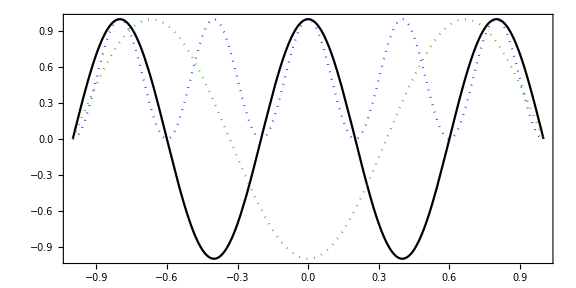

```mathematica
kk=3;
en=eigenvalues⟦kk⟧;
Ψ1=findFunction[en,v,L];
norm=√NIntegrate[Ψ1[x]^2,{x,-1,1}];
Ψ[x_]=Ψ1[x]/norm;
Plot[{Ψ[x],Ψ[x]^2,ISWell[x,kk]},{x,-1,1},PlotRange->All,PlotStyle->{Black,{Dotted,Blue},{Dotted,Darker[Green]}},AspectRatio->0.5,ImageSize->Large,Frame->True]
```

## Harmonic oscillator

```mathematica
l=15;
step=1;
max=30;
tollerance=10^-6;
Clear[v];
v[x_]=1/2 m ω^2 x^2;
Print["Time: ",Timing[eigenvalues=findAllEigenvaluesInf[v,step,max,tollerance,l];]⟦1⟧];
Print["Number of eigenvalues found: ",Length[eigenvalues]];
Print["E_exact=",eigenvalues];
```

Time: 3.32377

Number of eigenvalues found: 30

E_exact={0.499999,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5}

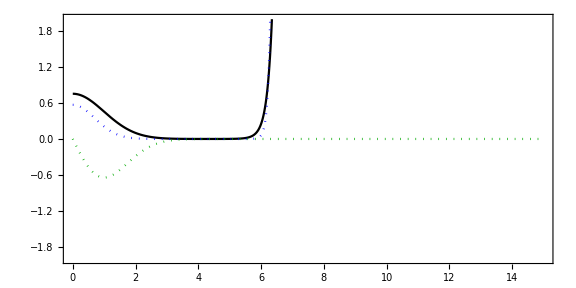

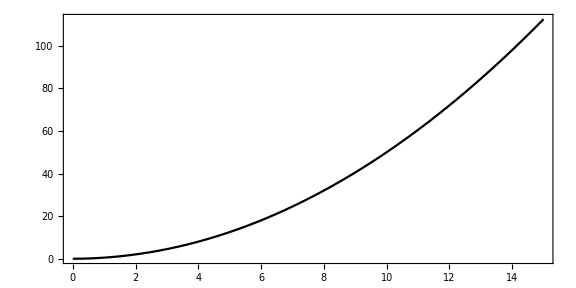

```mathematica
kk=1;
en=eigenvalues⟦kk⟧;
Ψ1=findFunctionInf[en,v,l,EvenQ[kk]];
norm=√NIntegrate[Ψ1[x]^2,{x,-2,2}]; (* This won't be correct *)
Ψ[x_]=Ψ1[x]/norm;
Plot[{Ψ[x],Ψ[x]^2,HarmonicWell[x,kk]},{x,0,l},PlotStyle->{Black,{Dotted,Blue},{Dotted,Darker[Green]}},AspectRatio->0.5,ImageSize->Large,Frame->True,PlotRange->{-2,2}]
Plot[v[x],{x,0,l},PlotStyle->{Black},AspectRatio->0.5,ImageSize->Large,Frame->True]
```

# Create figures

```mathematica
nevalues=30;
desiredMax=1.5;
emin=-1;
emax=30;
points=31;
range=10;
dX=0.05;
de=1;
```

```mathematica
eigenvaluesUP=Table[EnHE[k]//N,{k,0,nevalues}];
```

## Ti = 10, Tf = 1

```mathematica
Ti=10;
Tf=1;
```

### s = 1

```mathematica
s=1;
u1u1[x_]=MakeDSrFunction[eigenvaluesUP,s,Ti,Tf]//Simplify;
```

```mathematica
(*Quiet[Print["Time: ",Timing[perf1s1=TheoreticalPerformanceChangingStrength[u1u1,-desiredMax,desiredMax,points,Ti,Tf,1,de,emin,emax,tollerance,l];]⟦1⟧]]
{ticks1s1,ret1s1,pred1s1,dev1s1,ev1s1}=Transpose[perf1s1];
Ret1s1=Transpose[{ticks1s1,ret1s1}];
Pred1s1=Transpose[{ticks1s1,pred1s1}];
Ev1s1=Transpose[{ticks1s1,dev1s1}];*)
```

```mathematica
(*Export["saved2/Ret1s1.csv",Ret1s1];
Export["saved2/Pred1s1.csv",Pred1s1];
Export["saved2/Ev1s1.csv",Ev1s1];*)
```

```mathematica
Ret1s1=Import["saved2/Ret1s1.csv"];
Pred1s1=Import["saved2/Pred1s1.csv"];
Ev1s1=Import["saved2/Ev1s1.csv"];
```

### s = 3

```mathematica
s=3;
u1u3[x_]=MakeDSrFunction[eigenvaluesUP,s,Ti,Tf]//Simplify;
```

```mathematica
(*Quiet[Print["Time: ",Timing[perf1s3=TheoreticalPerformanceChangingStrength[u1u3,-desiredMax,desiredMax,points,Ti,Tf,3,de,emin,emax,tollerance,l];]⟦1⟧]]
{ticks1s3,ret1s3,pred1s3,dev1s3,ev1s3}=Transpose[perf1s3];
Ret1s3=Transpose[{ticks1s3,ret1s3}];
Pred1s3=Transpose[{ticks1s3,pred1s3}];
Ev1s3=Transpose[{ticks1s3,dev1s3}];*)
```

```mathematica
(*Export["saved2/Ret1s3.csv",Ret1s3];
Export["saved2/Pred1s3.csv",Pred1s3];
Export["saved2/Ev1s3.csv",Ev1s3];*)
```

```mathematica
Ret1s3=Import["saved2/Ret1s3.csv"];
Pred1s3=Import["saved2/Pred1s3.csv"];
Ev1s3=Import["saved2/Ev1s3.csv"];
```

### s = 7

```mathematica
s=7;
u1u7[x_]=MakeDSrFunction[eigenvaluesUP,s,Ti,Tf]//Simplify;
```

```mathematica
(*Quiet[Print["Time: ",Timing[perf1s7=TheoreticalPerformanceChangingStrength[u1u7,-desiredMax,desiredMax,points,Ti,Tf,7,de,emin,emax,tollerance,l];]⟦1⟧]]
{ticks1s7,ret1s7,pred1s7,dev1s7,ev1s7}=Transpose[perf1s7];
Ret1s7=Transpose[{ticks1s7,ret1s7}];
Pred1s7=Transpose[{ticks1s7,pred1s7}];
Ev1s7=Transpose[{ticks1s7,dev1s7}];*)
```

```mathematica
(*Export["saved2/Ret1s7.csv",Ret1s7];
Export["saved2/Pred1s7.csv",Pred1s7];
Export["saved2/Ev1s7.csv",Ev1s7];*)
```

```mathematica
Ret1s7=Import["saved2/Ret1s7.csv"];
Pred1s7=Import["saved2/Pred1s7.csv"];
Ev1s7=Import["saved2/Ev1s7.csv"];
```

## Ti = 1, Tf = 10

```mathematica
Ti=1;
Tf=10;
```

### s = 1

```mathematica
s=1;
u2u1[x_]=MakeDSrFunction[eigenvaluesUP,s,Ti,Tf]//Simplify;
```

```mathematica
(*Print["Time: ",Timing[perf2s1=TheoreticalPerformanceChangingStrength[u2u1,-desiredMax,desiredMax,points,Ti,Tf,1,de,emin,emax,tollerance,l];]⟦1⟧]
{ticks2s1,ret2s1,pred2s1,dev2s1,ev2s1}=Transpose[perf2s1];
Ret2s1=Transpose[{ticks2s1,ret2s1}];
Pred2s1=Transpose[{ticks2s1,pred2s1}];
Ev2s1=Transpose[{ticks2s1,dev2s1}];*)
```

```mathematica
(*Export["saved2/Ret2s1.csv",Ret2s1];
Export["saved2/Pred2s1.csv",Pred2s1];
Export["saved2/Ev2s1.csv",Ev2s1];*)
```

```mathematica
Ret2s1=Import["saved2/Ret2s1.csv"];
Pred2s1=Import["saved2/Pred2s1.csv"];
Ev2s1=Import["saved2/Ev2s1.csv"];
```

### s = 3

```mathematica
s=3;
u2u3[x_]=MakeDSrFunction[eigenvaluesUP,s,Ti,Tf]//Simplify;
```

```mathematica
(*Print["Time: ",Timing[perf2s3=TheoreticalPerformanceChangingStrength[u2u3,-desiredMax,desiredMax,points,Ti,Tf,3,de,emin,emax,tollerance,l];]⟦1⟧]
{ticks2s3,ret2s3,pred2s3,dev2s3,ev2s3}=Transpose[perf2s3];
Ret2s3=Transpose[{ticks2s3,ret2s3}];
Pred2s3=Transpose[{ticks2s3,pred2s3}];
Ev2s3=Transpose[{ticks2s3,dev2s3}];*)
```

```mathematica
(*Export["saved2/Ret2s3.csv",Ret2s3];
Export["saved2/Pred2s3.csv",Pred2s3];
Export["saved2/Ev2s3.csv",Ev2s3];*)
```

```mathematica
Ret2s3=Import["saved2/Ret2s3.csv"];
Pred2s3=Import["saved2/Pred2s3.csv"];
Ev2s3=Import["saved2/Ev2s3.csv"];
```

### s = 7

```mathematica
s=7;
u2u7[x_]=MakeDSrFunction[eigenvaluesUP,s,Ti,Tf]//Simplify;
```

```mathematica
(*Print["Time: ",Timing[perf2s7=TheoreticalPerformanceChangingStrength[u2u7,-desiredMax,desiredMax,points,Ti,Tf,7,de,emin,emax,tollerance,l];]⟦1⟧]
{ticks2s7,ret2s7,pred2s7,dev2s7,ev2s7}=Transpose[perf2s7];
Ret2s7=Transpose[{ticks2s7,ret2s7}];
Pred2s7=Transpose[{ticks2s7,pred2s7}];
Ev2s7=Transpose[{ticks2s7,dev2s7}];*)
```

```mathematica
(*Export["saved2/Ret2s7.csv",Ret2s7];
Export["saved2/Pred2s7.csv",Pred2s7];
Export["saved2/Ev2s7.csv",Ev2s7];*)
```

```mathematica
Ret2s7=Import["saved2/Ret2s7.csv"];
Pred2s7=Import["saved2/Pred2s7.csv"];
Ev2s7=Import["saved2/Ev2s7.csv"];
```

## Ti = 10, Tf = 1 - Prediction

```mathematica
Ti=10;
Tf=1;
```

### s = 1

```mathematica
s=1;
u3u1[x_]=MakeDStFunction[eigenvaluesUP,s,Ti,Tf]//Simplify;
```

```mathematica
(*Print["Time: ",Timing[perf3s1=TheoreticalPerformanceChangingStrength[u3u1,-desiredMax,desiredMax,points,Ti,Tf,1,de,emin,emax,tollerance,l];]⟦1⟧]
{ticks3s1,ret3s1,pred3s1,dev3s1,ev3s1}=Transpose[perf3s1];
Ret3s1=Transpose[{ticks3s1,ret3s1}];
Pred3s1=Transpose[{ticks3s1,pred3s1}];
Ev3s1=Transpose[{ticks3s1,dev3s1}];*)
```

```mathematica
(*Export["saved2/Ret3s1.csv",Ret3s1];
Export["saved2/Pred3s1.csv",Pred3s1];
Export["saved2/Ev3s1.csv",Ev3s1];*)
```

```mathematica
Ret3s1=Import["saved2/Ret3s1.csv"];
Pred3s1=Import["saved2/Pred3s1.csv"];
Ev3s1=Import["saved2/Ev3s1.csv"];
```

### s = 3

```mathematica
s=3;
u3u3[x_]=MakeDStFunction[eigenvaluesUP,s,Ti,Tf]//Simplify;
```

```mathematica
(*Print["Time: ",Timing[perf3s3=TheoreticalPerformanceChangingStrength[u3u3,-desiredMax,desiredMax,points,Ti,Tf,3,de,emin,emax,tollerance,l];]⟦1⟧]
{ticks3s3,ret3s3,pred3s3,dev3s3,ev3s3}=Transpose[perf3s3];
Ret3s3=Transpose[{ticks3s3,ret3s3}];
Pred3s3=Transpose[{ticks3s3,pred3s3}];
Ev3s3=Transpose[{ticks3s3,dev3s3}];*)
```

```mathematica
(*Export["saved2/Ret3s3.csv",Ret3s3];
Export["saved2/Pred3s3.csv",Pred3s3];
Export["saved2/Ev3s3.csv",Ev3s3];*)
```

```mathematica
Ret3s3=Import["saved2/Ret3s3.csv"];
Pred3s3=Import["saved2/Pred3s3.csv"];
Ev3s3=Import["saved2/Ev3s3.csv"];
```

### s = 7

```mathematica
s=7;
u3u7[x_]=MakeDStFunction[eigenvaluesUP,s,Ti,Tf]//Simplify;
```

```mathematica
(*Print["Time: ",Timing[perf3s7=TheoreticalPerformanceChangingStrength[u3u7,-desiredMax,desiredMax,points,Ti,Tf,7,de,emin,emax,tollerance,l];]⟦1⟧]
{ticks3s7,ret3s7,pred3s7,dev3s7,ev3s7}=Transpose[perf3s7];
Ret3s7=Transpose[{ticks3s7,ret3s7}];
Pred3s7=Transpose[{ticks3s7,pred3s7}];
Ev3s7=Transpose[{ticks3s7,dev3s7}];*)
```

```mathematica
(*Export["saved2/Ret3s7.csv",Ret3s7];
Export["saved2/Pred3s7.csv",Pred3s7];
Export["saved2/Ev3s7.csv",Ev3s7];*)
```

```mathematica
Ret3s7=Import["saved2/Ret3s7.csv"];
Pred3s7=Import["saved2/Pred3s7.csv"];
Ev3s7=Import["saved2/Ev3s7.csv"];
```

Create figures

### Consolidate data

```mathematica
sc={#⟦1⟧,100#⟦2⟧}&;
ch=Abs[#⟦1⟧]<10^-8&;
```

```mathematica
points=31;
```

```mathematica
dRet1s1=sc/@(Ret1s1-Table[{0,Last@Last@Select[Ret1s1,ch]},{points}]);
dRet1s3=sc/@(Ret1s3-Table[{0,Last@Last@Select[Ret1s3,ch]},{points}]);
dRet1s7=sc/@(Ret1s7-Table[{0,Last@Last@Select[Ret1s7,ch]},{points}]);
dPred1s1=sc/@(Pred1s1-Table[{0,Last@Last@Select[Pred1s1,ch]},{points}]);
dPred1s3=sc/@(Pred1s3-Table[{0,Last@Last@Select[Pred1s3,ch]},{points}]);
dPred1s7=sc/@(Pred1s7-Table[{0,Last@Last@Select[Pred1s7,ch]},{points}]);
```

```mathematica
dRet2s1=sc/@(Ret2s1-Table[{0,Last@Last@Select[Ret2s1,ch]},{points}]);
dRet2s3=sc/@(Ret2s3-Table[{0,Last@Last@Select[Ret2s3,ch]},{points}]);
dRet2s7=sc/@(Ret2s7-Table[{0,Last@Last@Select[Ret2s7,ch]},{points}]);
dPred2s1=sc/@(Pred2s1-Table[{0,Last@Last@Select[Pred2s1,ch]},{points}]);
dPred2s3=sc/@(Pred2s3-Table[{0,Last@Last@Select[Pred2s3,ch]},{points}]);
dPred2s7=sc/@(Pred2s7-Table[{0,Last@Last@Select[Pred2s7,ch]},{points}]);
```

```mathematica
dRet3s1=sc/@(Ret3s1-Table[{0,Last@Last@Select[Ret3s1,ch]},{points}]);
dRet3s3=sc/@(Ret3s3-Table[{0,Last@Last@Select[Ret3s3,ch]},{points}]);
dRet3s7=sc/@(Ret3s7-Table[{0,Last@Last@Select[Ret3s7,ch]},{points}]);
dPred3s1=sc/@(Pred3s1-Table[{0,Last@Last@Select[Pred3s1,ch]},{points}]);
dPred3s3=sc/@(Pred3s3-Table[{0,Last@Last@Select[Pred3s3,ch]},{points}]);
dPred3s7=sc/@(Pred3s7-Table[{0,Last@Last@Select[Pred3s7,ch]},{points}]);
```

```mathematica
l=8;
normInt=Quiet[NIntegrate[(#[x])^2,{x,-l,l}]^(1/2)&];
Quiet[n1u1=normInt[u1u1]];
Quiet[n1u3=normInt[u1u3]];
Quiet[n1u7=normInt[u1u7]];
Quiet[n2u1=normInt[u2u1]];
Quiet[n2u3=normInt[u2u3]];
Quiet[n2u7=normInt[u2u7]];
Quiet[n3u1=normInt[u3u1]];
Quiet[n3u3=normInt[u3u3]];
Quiet[n3u7=normInt[u3u7]];
```

## Using scifig.

```mathematica
AppendTo[$Path,"/Users/nathaniel/Nathaniel/Programs/Mathematica/SciDraw-0.0.7/packages"];
Quiet[Get["SciDraw`"]]
```

𝒮𝒸𝒾𝒟𝓇𝒶𝓌: Publication–quality scientific figures with Mathematica
M. A. Caprio, University of Notre Dame
Version 0.0.7 (March 28, 2015)
View color paletteVisit home page  -Graphics-

```mathematica
lineStyle={Magenta,{Dotted,Blue,Thick},{AbsoluteDashing[{12,4}],Black}};
```

```mathematica
thickness=0.3;
lineStyle={{Magenta,AbsoluteThickness[thickness]},{Blue,AbsoluteDashing[{1,1}],AbsoluteThickness[thickness]},{AbsoluteDashing[{3,1}],Black,AbsoluteThickness[thickness]}};
```

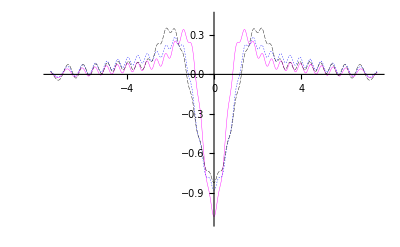

```mathematica
Plot[{u1u1[x]/n1u1,u1u3[x]/n1u3,u1u7[x]/n1u7},{x,-range/2,range/2},PlotStyle->lineStyle,PlotRange->{-1.12,0.44}]
```

```mathematica
font=8;
combinedOptimizationPerf=Show[
Figure[
Multipanel[
{
(* panel (a) *)
FigurePanel[
{
FigGraphics[
Plot[{u1u1[x]/n1u1,u1u3[x]/n1u3,u1u7[x]/n1u7},{x,-range/2,range/2},PlotStyle->lineStyle]
]
},{1,1},
XShowTickLabels->False,
XPlotRange->{-range/2,range/2},
YPlotRange->{-1.12,0.44},
YFrameLabel->textit["u_p(x)=U(x)/|U|"]
];

(* panel (b) *)
FigurePanel[
{
FigGraphics[
ListLinePlot[{dRet1s1,dRet1s3,dRet1s7},PlotStyle->lineStyle]
]
},
{1,2},
XShowTickLabels->False,
ExteriorEdgeMask->True,
XPlotRange->{-1.5,1.5},
YPlotRange->{-1.6,1.6},
YFrameLabel->"Δ% - retrodiction"
];

(* panel (c) *)
FigurePanel[
{
FigGraphics[
ListLinePlot[{dPred1s1,dPred1s3,dPred1s7},PlotStyle->lineStyle]
]
},
{1,3},
XShowTickLabels->False,
ExteriorEdgeMask->True,
XPlotRange->{-1.5,1.5},
YPlotRange->{-4.2,4.2},
YFrameLabel->"Δ% - prediction"
];

(* panel (d) *)
FigurePanel[
{
FigGraphics[
Plot[{u2u1[x]/n2u1,u2u3[x]/n2u3,u2u7[x]/n2u7},{x,-range/2,range/2},PlotStyle->lineStyle]
]
},
{2,1},
XShowTickLabels->False,
XPlotRange->{-range/2,range/2},
YPlotRange->{-0.6,0.8},
XFrameLabel->None,
YFrameLabel->textit["u_p(x)=U(x)/|U|"]
];

(* panel (e) *)
FigurePanel[
{
FigGraphics[
ListLinePlot[{dRet2s1,dRet2s3,dRet2s7},PlotStyle->lineStyle]
]
},
{2,2},
XShowTickLabels->False,
XPlotRange->{-1.5,1.5},
YPlotRange->{-5,5},
YFrameLabel->"Δ% - retrodiction"
];

(* panel (f) *)
FigurePanel[
{
FigGraphics[
ListLinePlot[{dPred2s1,dPred2s3,dPred2s7},PlotStyle->lineStyle]
]
},
{2,3},
XShowTickLabels->False,
XPlotRange->{-1.5,1.5},
YPlotRange->{-0.62,0.62},
YFrameLabel->"Δ% - prediction"
];

(* panel (g) *)
FigurePanel[
{
FigGraphics[
Plot[{u3u1[x]/n3u1,u3u3[x]/n3u3,u3u7[x]/n3u7},{x,-range/2,range/2},PlotStyle->lineStyle]
]
},
{3,1},
XShowTickLabels->True,
XFrameLabel->textit["x"],
XPlotRange->{-range/2,range/2},
YPlotRange->{-1.2,0.5},
YFrameLabel->textit["u_p(x)=U(x)/|U|"]
];

(* panel (h) *)
FigurePanel[
{
FigGraphics[
ListLinePlot[{dRet3s1,dRet3s3,dRet3s7},PlotStyle->lineStyle]
]
},
{3,2},
XPlotRange->{-1.5,1.5},
YPlotRange->{-1.6,1.6},
XShowTickLabels->True,
XFrameLabel->"Strength, "textit["λ"],
YFrameLabel->"Δ% - retrodiction"
];

(* panel (i) *)
FigurePanel[
{
FigGraphics[
ListLinePlot[{dPred3s1,dPred3s3,dPred3s7},PlotStyle->lineStyle]
]
},
{3,3},
XPlotRange->{-1.5,1.5},
YPlotRange->{-4.2,4.2},
XShowTickLabels->True,
XFrameLabel->"Strength, "textit["λ"],
YFrameLabel->"Δ% - prediction"
];

},
Dimensions->{3,3},
(* panel appearance *)
Background->None,YShowTickLabels->True,
TickFontSize->font,
(* frame lettering *)
FrameFontSize->font,
(* panel lettering *)
PanelLetterFontSize->font,PanelLetterDelimiters->{"",""},PanelLetterPosition->{TopLeft,8},
(* panel geometry *)
XPanelSizes->{4.75,2,2},XPanelGaps->0.7,YPanelGaps->0.1,
(* so Y labels can be used for panels other than the first column*)
ExteriorEdgeMask->True
],
CanvasSize->{7,4.5}
],
(* insert line legend *)
Epilog->{
Inset[
LineLegend[{Directive[Magenta,Thin],Directive[Blue,Thin],Directive[Black,Thin]},{"t=1","t=3","t=7"},LegendLayout->"Row",LabelStyle->font,LegendMarkerSize->10]
,Scaled[{0.2,0.2}]]}
]
```

-Graphics-

```mathematica
(*Export["combinedOptimizationPerf.eps",combinedOptimizationPerf,"CompressionLevel"->0];*)
```

# Other stuff

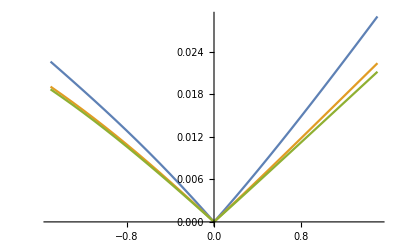

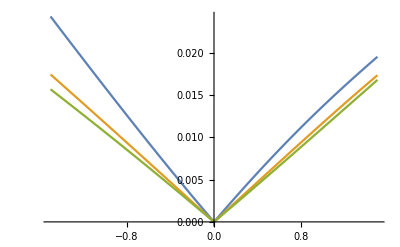

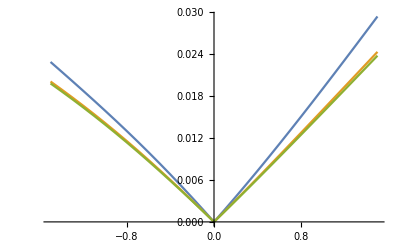

```mathematica
ListLinePlot[{Ev1s1,Ev1s3,Ev1s7},PlotRange->All]
ListLinePlot[{Ev2s1,Ev2s3,Ev2s7},PlotRange->All]
ListLinePlot[{Ev3s1,Ev3s3,Ev3s7},PlotRange->All]
```

```mathematica
AbsDif[lst_]:=Table[Sum[Abs[lst⟦i,j⟧-lst⟦i,j-1⟧-1],{j,2,Length[lst⟦i⟧]}],{i,1,Length[lst]}]
MaxDif[lst_]:=Table[Max[Table[Abs[lst⟦i,j⟧-lst⟦i,j-1⟧-1],{j,2,Length[lst⟦i⟧]}]],{i,1,Length[lst]}]
```

```mathematica
absdif1s1=AbsDif[ev1s1];
absdif1s3=AbsDif[ev1s3];
absdif1s7=AbsDif[ev1s7];
absdif2s1=AbsDif[ev2s1];
absdif2s3=AbsDif[ev2s3];
absdif2s7=AbsDif[ev2s7];
absdif3s1=AbsDif[ev3s1];
absdif3s3=AbsDif[ev3s3];
absdif3s7=AbsDif[ev3s7];
```

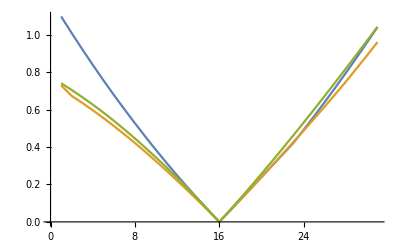

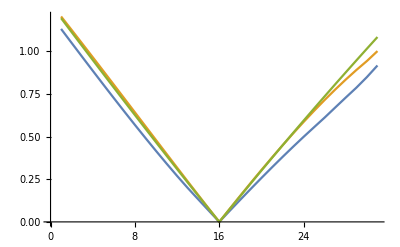

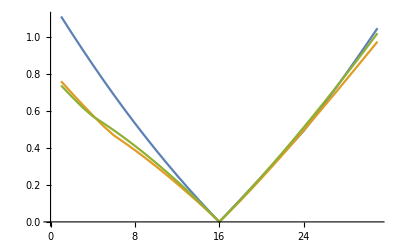

```mathematica
ListLinePlot[{absdif1s1,absdif1s3,absdif1s7}]
ListLinePlot[{absdif2s1,absdif2s3,absdif2s7}]
ListLinePlot[{absdif3s1,absdif3s3,absdif3s7}]
```

# Ti = 5, Tf = 5

```mathematica
Ti=5;
Tf=5;
```

```mathematica
desiredMax=0.5;
points=31;
de=1;
```

### s = 1

```mathematica
s=1;
u4u1[x_]=MakeDStFunction[eigenvaluesUP,s,Ti,Tf]//Simplify;
```

```mathematica
Print["Time: ",Timing[perf4s1=TheoreticalPerformanceChangingStrength[u4u1,-desiredMax,desiredMax,points,Ti,Tf,1,de,max,tollerance,l];]⟦1⟧]
{ticks4s1,ret4s1,pred4s1,nev4s1}=Transpose[perf4s1];
Ret4s1=Transpose[{ticks4s1,ret4s1}];
Pred4s1=Transpose[{ticks4s1,pred4s1}];
```

Time: 210.741

### s = 3

```mathematica
s=3;
u4u3[x_]=MakeDStFunction[eigenvaluesUP,s,Ti,Tf]//Simplify;
```

```mathematica
Print["Time: ",Timing[perf4s3=TheoreticalPerformanceChangingStrength[u4u3,-desiredMax,desiredMax,points,Ti,Tf,3,de,max,tollerance,l];]⟦1⟧]
{ticks4s3,ret4s3,pred4s3,nev4s3}=Transpose[perf4s3];
Ret4s3=Transpose[{ticks4s3,ret4s3}];
Pred4s3=Transpose[{ticks4s3,pred4s3}];
```

Time: 176.344

### s = 7

```mathematica
s=7;
u4u7[x_]=MakeDStFunction[eigenvaluesUP,s,Ti,Tf]//Simplify;
```

```mathematica
Print["Time: ",Timing[perf4s7=TheoreticalPerformanceChangingStrength[u4u7,-desiredMax,desiredMax,points,Ti,Tf,7,de,max,tollerance,l];]⟦1⟧]
{ticks4s7,ret4s7,pred4s7,nev4s7}=Transpose[perf4s7];
Ret4s7=Transpose[{ticks4s7,ret4s7}];
Pred4s7=Transpose[{ticks4s7,pred4s7}];
```

Time: 206.452

```mathematica
dRet4s1=sc/@(Ret4s1-Table[{0,Last@Last@Select[Ret4s1,ch]},{points}]);
dRet4s3=sc/@(Ret4s3-Table[{0,Last@Last@Select[Ret4s3,ch]},{points}]);
dRet4s7=sc/@(Ret4s7-Table[{0,Last@Last@Select[Ret4s7,ch]},{points}]);
dPred4s1=sc/@(Pred4s1-Table[{0,Last@Last@Select[Pred4s1,ch]},{points}]);
dPred4s3=sc/@(Pred4s3-Table[{0,Last@Last@Select[Pred4s3,ch]},{points}]);
dPred4s7=sc/@(Pred4s7-Table[{0,Last@Last@Select[Pred4s7,ch]},{points}]);
```

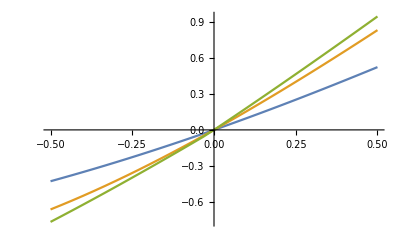

-Graphics-

```mathematica
ListLinePlot[{dRet4s1,dRet4s3,dRet4s7}]
ListLinePlot[{dPred4s1,dPred4s3,dPred4s7}]
```

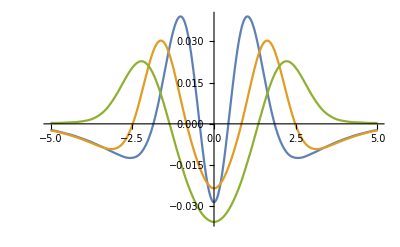

```mathematica
Plot[{u4u1[x],u4u3[x],u4u7[x]},{x,-5,5}]
```